# RQA Exploration

Alison Ord

Flip Phillips

## Load FP’s RQA package

```mathematica
gitHubDir=ResourceFunction["NotebookRelativePath"][{"..","..","..","RQA","RQA"}]
```

C:\Users\Alison\Documents\GitHub\WSS2019-ao\Final Project\Drafts\..\..\..\RQA\RQA

```mathematica
Get[FileNameJoin[{gitHubDir,"RQA.wl"}]]
```

```mathematica
?RQA`*
```

```mathematica
data=Flatten[Import[ResourceFunction["NotebookRelativePath"][{"..","Data","rock4z.dat"}]]];
```

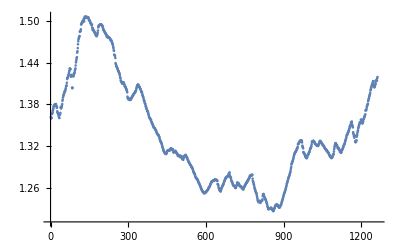

```mathematica
ListPlot[data]
```

```mathematica
ds=RQAMakeTimeSeries[data,1,1]
```

TimeSeries[…]

```mathematica
lag=RQAEstimateLag[ds]
```

305.726

```mathematica
lag=10
```

10

```mathematica
RQAEstimateDimensionality[ds,lag]
```

4.72984×10^-7

{Null,{{{2,0.40655,1262,4.72984×10^-8,1252,1.41325×10^-6},{3,0.0990338,1252,1.41325×10^-6,1242,2.94388×10^-6},{4,0.023539,1242,2.94388×10^-6,1232,4.36527×10^-6}}}}

```mathematica
embedding=RQAEmbed[ds,3,lag]
```

TimeSeries[…]

What do you have to do to read these numbers?

```mathematica
ParametricPlot3D[embedding[t],{t,1,650}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[embedding[t],{t,1,1222},PlotStyle->{Orange,Specularity[White,10]}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[embedding[t],{t,1,1222},PlotStyle->Directive[Green,Opacity[0.8],Specularity[White,20]]]
```

-Graphics3D-

These give you information on the neighbours, nearestneighbours and neighbours, but what is it you really need to know? Number of nearest neighbours? & don’t you normally (in VRA) search for these earlier while determining the dimensionality?

```mathematica
rn=RQANeighbors[embedding];
```

```mathematica
rnn=RQANearestNeighbors[embedding];
```

```mathematica
rnd=RQANeighborDistances[embedding];
```

```mathematica
rm=RQARecurrenceMap[embedding];
```

```mathematica
Dimensions[rm]
```

{1242,1242}

```mathematica
First[Dimensions[rm]]
```

1242

```mathematica
MatrixPlot[rm,DataReversed->{True,False},PlotRange->All,ColorFunction->(RGBColor[1-#,#,1/2]&)]
```

-Graphics-

```mathematica
MinMax[rm]
```

{0,1}

```mathematica
dm=RQADistanceMap[embedding];
```

```mathematica
MatrixPlot[dm,DataReversed->{True,False},PlotRange->All,ColorFunction->Hue]
```

-Graphics-

```mathematica
MinMax[dm]
```

{0.,0.224875}

```mathematica
rec=N[RQARecurrence[rm]]
```

0.680771

%REC=40.2 Result from RQA for embedding dimension of 3 and a lag of 10

```mathematica
det=N[RQADeterminism[rm]]
```

0.999567

%DET=99.9 Result from RQA

```mathematica
lam=N[RQALaminarity[rm,3]]
```

0.999178

%LAM=100 Result from RQA

```mathematica
trap=N[RQATrappingTime[rm]]
```

220.737

TT=121.8 Result from RQA

```mathematica
trend=N[RQATrend[rm]]
```

General::munfl: Exp[-3203.58] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1413.91] is too small to represent as a normalized machine number; precision may be lost.

-30.6973

Trend -56.4 Result from RQA

```mathematica
entropy=N[RQAEntropy[rm]]
```

8.02657

Entropy 7.6 Result from RQA

```mathematica
chaos=N[RQAChaos[rm]]
```

0.000805802

Result from RQA ???

First pass code for calculating DMAX. It should be easy to derive from DET as only wanting the sum of the length segments of the diagonal; don’t need to divide that number by the total number recurrent plots.

```mathematica
RQADmax[rm_,thresh_:2]:=Module[{ut,w,diags,segLens,lens,nRP},ut=UpperTriangularize[rm,1];
w=First[Dimensions[rm]];
diags=Diagonal[ut,#]&/@Range[1,w-1];
segLens=segmentLengths[diags,thresh];
lens=Total/@segLens;
Max[lens]
]/;SquareMatrixQ[rm]
```

```mathematica
N[RQADmax[rm,2]]
```

1241.

Similarly here for VMAX. The segment lengths are for the verticals. why the word lens?

```mathematica
RQAVmax[rm_,thresh_:2]:=Module[{ut,verts,segLens,lens,nRP},ut=UpperTriangularize[rm,1];
verts=Transpose[ut];
segLens=segmentLengths[verts,thresh];
lens=Total/@segLens;
Total[lens]
]/;SquareMatrixQ[rm]
```

```mathematica
RQAVmax[rm,3]
```

Total[segmentLengths[{881,892,887,895,869,886,885,884,871,871,862,873,876,885,862,880,878,878,842,853,852,869,869,875,842,844,842,826,792,796,791,789,785,778,778,786,790,796,797,796,795,796,794,803,805,801,796,790,785,780,772,765,745,707,700,699,693,718,713,688,683,661,710,679,669,580,567,621,614,578,570,552,623,597,580,511,485,519,507,459,453,450,464,448,442,427,412,399,391,374,369,361,347,341,338,329,321,311,307,303,298,297,290,287,285,281,276,269,267,267,263,261,251,250,254,251,244,221,218,220,215,209,207,206,210,205,204,205,200,206,202,199,201,200,200,200,200,201,203,202,215,219,219,219,224,224,224,224,224,223,227,228,227,227,227,227,226,226,225,224,225,225,222,220,220,219,218,217,216,215,214,210,209,207,205,204,202,203,202,199,198,197,196,195,194,193,191,191,190,189,188,188,188,188,187,188,187,188,187,186,187,188,187,187,186,187,188,187,186,186,187,186,188,187,187,187,187,186,185,185,187,188,190,192,192,194,195,195,195,197,207,207,207,209,210,214,216,217,227,236,260,263,268,272,273,276,276,277,279,283,341,352,356,367,377,390,411,420,438,446,477,481,488,502,508,529,530,533,536,540,550,552,556,558,560,563,566,567,566,565,566,565,565,566,567,569,573,573,572,572,572,571,570,569,568,569,571,570,569,567,567,564,562,561,560,559,557,554,553,551,548,545,542,539,538,536,534,531,530,530,526,525,522,520,519,519,516,515,516,516,515,512,511,511,512,511,511,511,512,516,515,514,515,517,518,518,520,520,522,526,526,525,527,527,536,541,555,572,580,604,612,617,642,647,665,685,720,724,728,736,741,744,756,756,756,758,759,759,760,760,761,761,760,763,765,772,777,784,789,792,795,794,794,798,798,799,801,806,810,810,816,826,828,836,837,836,835,834,833,832,831,830,829,828,827,826,825,824,823,822,821,820,819,818,817,816,815,814,813,812,811,810,809,808,807,806,805,804,803,802,801,800,799,798,797,796,795,794,793,792,791,790,789,788,787,786,785,784,783,782,781,780,779,778,777,776,775,774,773,772,771,770,769,768,767,766,765,764,763,762,761,760,759,758,757,756,755,754,753,751,750,749,748,747,747,746,744,744,742,741,740,739,738,737,736,735,734,733,729,728,727,724,722,721,720,718,717,716,715,714,712,711,710,708,706,705,703,700,696,694,693,692,690,688,687,685,684,682,680,679,677,676,674,672,671,669,668,667,666,664,662,661,660,658,656,655,653,652,650,649,647,645,643,642,640,639,638,637,636,634,632,630,627,626,625,623,622,621,618,617,616,615,614,613,612,611,610,609,608,607,606,606,605,605,605,604,605,605,605,605,604,603,602,601,600,599,599,598,598,597,597,596,596,595,594,593,592,592,591,590,589,588,587,586,584,583,582,581,579,577,576,575,573,572,570,569,568,567,566,565,564,563,562,561,560,559,558,557,556,555,554,553,552,552,551,551,549,550,550,549,549,548,547,547,546,546,546,545,544,544,544,542,541,540,539,538,537,536,534,534,533,530,529,527,526,525,523,522,521,520,519,517,515,513,512,511,510,508,507,507,506,505,503,501,500,499,498,497,496,496,495,493,492,491,490,489,488,487,486,485,484,483,482,481,480,479,478,477,476,475,474,473,472,471,470,469,468,467,466,466,465,464,464,463,463,463,462,461,461,461,460,459,458,458,457,457,456,455,454,453,451,449,448,447,446,445,443,442,441,439,436,435,433,431,430,429,427,425,421,417,415,413,412,411,410,408,403,400,398,397,396,395,393,392,391,390,388,387,387,385,385,384,383,381,380,379,377,377,377,376,375,375,373,371,369,367,365,364,364,362,360,359,357,354,347,345,334,332,329,326,322,321,314,312,308,304,299,298,295,294,293,292,291,291,291,290,290,289,289,288,289,289,288,287,286,286,285,283,282,281,280,279,278,278,281,285,285,285,284,283,288,288,288,287,289,292,297,302,302,301,301,301,301,300,300,300,300,299,299,300,302,303,302,303,302,303,305,306,306,305,305,305,305,305,305,304,305,305,305,305,304,304,304,305,304,304,304,305,305,305,306,308,307,307,307,307,307,306,310,311,311,310,309,308,307,306,305,304,303,302,301,300,299,298,297,296,295,294,293,292,291,290,289,288,287,286,285,284,283,282,281,280,279,278,277,276,275,274,273,272,271,270,269,268,267,266,265,264,263,262,261,260,259,258,257,256,255,254,253,252,251,250,249,248,247,246,245,244,243,242,241,240,239,238,237,236,235,234,233,232,231,230,229,228,227,226,225,224,223,222,221,220,219,218,217,216,215,214,213,212,211,210,209,208,207,206,205,204,203,202,201,200,199,198,197,196,195,194,193,192,191,190,189,188,187,186,185,184,183,182,181,180,179,178,177,176,175,174,173,172,171,170,169,168,167,166,165,164,163,162,161,160,159,158,157,156,155,154,153,152,151,150,149,148,147,146,145,144,143,142,141,140,139,138,137,136,135,134,133,132,131,130,129,128,127,126,125,124,123,122,121,120,119,118,117,116,115,114,113,112,111,110,109,108,107,106,105,104,103,102,101,100,99,98,97,96,95,94,93,92,91,90,89,88,87,86,85,84,83,82,81,80,79,78,77,76,75,74,73,72,71,70,69,68,67,66,65,64,63,62,61,60,59,58,57,56,55,54,53,52,51,50,49,48,47,46,45,44,43,42,41,40,39,38,37,36,35,34,33,32,31,30,29,28,27,26,25,24,23,22,21,20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,0},3]]

```mathematica
N[RQAVmax[rm,3]]
```

```mathematica
Head[%]
```

Total

```mathematica
RQADetnew[rm_,thresh_:2]:=Module[{ut,w,diags,segLens,lens,nRP},ut=UpperTriangularize[rm,1];
w=First[Dimensions[rm]];
diags=Diagonal[ut,#]&/@Range[1,w-1];
segLens=segmentLengths[diags,thresh];
lens=Total/@segLens;
nRP=Total[Flatten[ut]];
Total[lens]/nRP]/;SquareMatrixQ[rm]
```

```mathematica
rec=N[RQADetnew[rm]]
```

Total::tllen: Lists of unequal length in {{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,«1191»},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,«1190»},«47»,{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,«1142»},«1191»} cannot be added.

Total::tllen: Lists of unequal length in {{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,«1191»},«49»,«1191»} cannot be added.

1.90605×10^-6 Total[segmentLengths[Total[{1}],2.]]
 |  |  |  |

```mathematica
RQARecurnew[rm_]:=Module[{ut,w,nMax,nRP},ut=UpperTriangularize[rm,1];
w=First[Dimensions[rm]];
nMax=(w (w-1)/2);
nRP=Total[Flatten[ut]];
nRP/nMax]/;SquareMatrixQ[rm]
runLength[list_]:={First[#],Length[#]}&/@Split[list]
segmentLengths[m_,tLen_:2]:=Module[{rl,selFun,n},rl=runLength/@m;
selFun=Select[#[[1]]==1∧#[[2]]≥tLen&];
(selFun/@rl)/.{{}->{0},{1,n_}->n}]
```

```mathematica
rec=N[RQARecurnew[rm]]
```

0.680771

Marwan&Webber Equation 1.11

```mathematica
RQARatio=det/rec
```

1.46829